```mathematica
NN = 15

m0[a_] := ⅇ^(1/NN Log[a])

σ0[a_] := ⅇ^(1/NN Log[ 1 + a])



mj[a_,j_] := m0[a] ⅇ^(2 π ⅈ j / NN)

m1[a_] := m0[a] ⅇ^(2 π ⅈ  / NN)

σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)



W0[a_] := (- 1)/(2π)( NN σ0[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ0[a] - mj[a,j] ])



W1[a_] := -1/(2π) (NN σ1[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ1[a] - mj[a,j] ] )



Tower[a_, k_] := (( ⅇ^(2 π ⅈ / NN) - 1 ) W0[a] + ⅈ mj[a,k])/(m1[a] - m0[a])

rmax = ⅇ^2
logz[x_,y_] := ⅇ^(ⅈ Arg[ x + ⅈ y]) (x^2 + y^2)^(NN/2)
```

15

ⅇ^2

```mathematica
rad[k_] := ⅇ^(1 - Cos[π ( 2 k - 1 ) / NN])
```

```mathematica
rad[Ceiling[NN/2]]  // N
```

7.38906

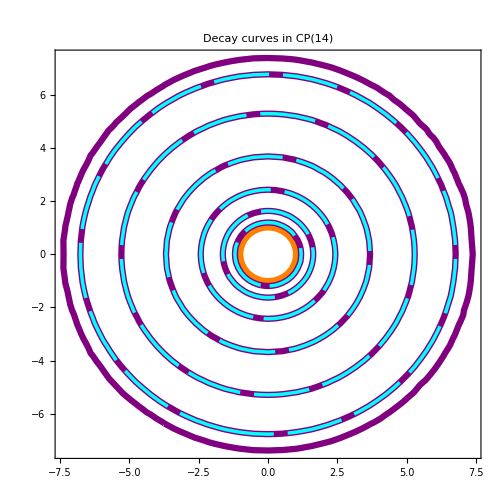

```mathematica
ContourPlot[    Evaluate[   Table[ Re[ Tower[ logz[x, y], j] ] == 0 , { j, NN -1} ]   ], 
                             { x , -rmax, rmax}, { y, -rmax, rmax },
                             ContourStyle->
                          Join[ { Directive[ Thickness[0.009], Orange ]  },
                       Table[ Directive[ Thickness[0.009], Purple ], {k,Ceiling[NN/2] -1 }] ,
                       Table[ Directive[ Thickness[0.005],Cyan, Dashing->{0.08,0.02} ], {k,NN -1 - Ceiling[NN/2] }] ] ,
                            PlotLabel-> Style["Decay curves in CP(14)",FontSize->24], LabelStyle->Directive[FontSize->18]]
```

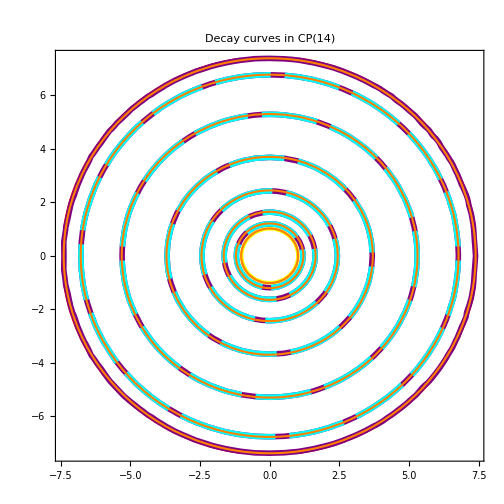

```mathematica
ContourPlot[    Evaluate[Join[  { x^2+y^2  == 1.02 ⅇ^4 },  Table[ Re[ Tower[ logz[x, y], j] ] == 0 , { j, NN -1 } ] ,
                                                                                                              Table[ x^2 + y^2 == ( ⅇ^(1 - Cos[π ( 2 k - 1 ) / NN]))^2, { k, Ceiling[NN/2]} ] ]], 
                              { x , -rmax, rmax}, { y, -rmax, rmax },
                             ContourStyle->
                          Join[ { Directive[ Thickness[0.002], Red ], Directive[ Thickness[0.005], Yellow ]  },
                       Table[ Directive[ Thickness[0.008], Purple ], {k,Ceiling[NN/2]-1} ],
                       Table[ Directive[ Thickness[0.008], Cyan,Dashing->{0.08,0.02}  ], {k,NN - 1 - Ceiling[NN/2]} ],
                     Table[ Directive[ Thickness[0.003], Orange], {k,Ceiling[NN/2]}]       ] ,
                          PlotLabel-> Style["Decay curves in CP(14)",FontSize->24], LabelStyle->Directive[FontSize->18] ]
```

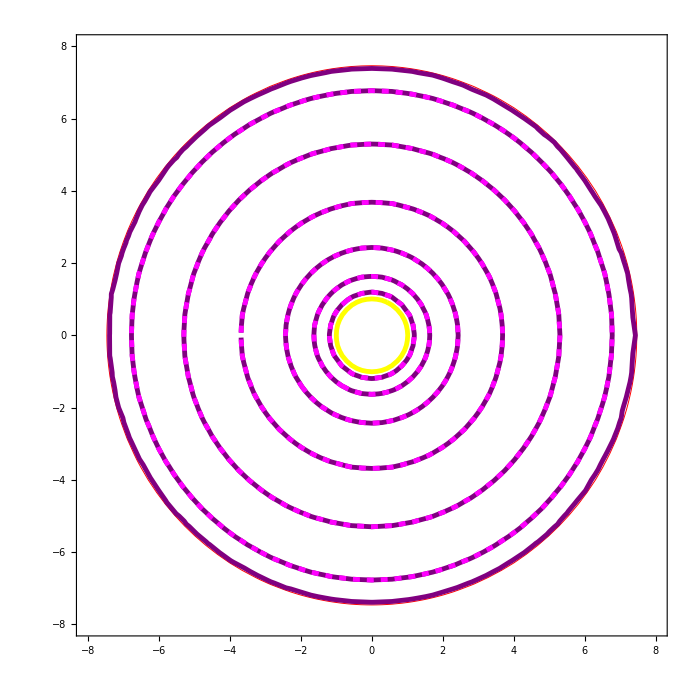

```mathematica
ContourPlot[    Evaluate[Join[  { x^2+y^2  == 1.02 ⅇ^4 },  Table[ Re[ Tower[ logz[x, y], j] ] == 0 , { j, NN -1 } ] ]
                                                                                                              ], 
                             { x , -8, 8}, {y, -8, 8},
                             ContourStyle->
                          Join[ { Directive[ Thickness[0.001], Red ], Directive[ Thickness[0.005], Yellow ]  },
                       Table[ Directive[ Thickness[0.005], Purple ], {k,Ceiling[NN/2]-1} ],
                       Table[ Directive[ Thickness[0.005], Magenta,Dashed ], {k,NN - 1 - Ceiling[NN/2]} ]          ]  ]
```

```mathematica
FindRoot[ Re[ Tower[x, 2] ], {x, 10.} ]
```

{x→14.3649}

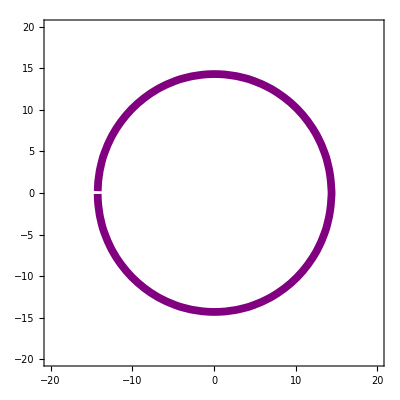

```mathematica
L = 20;
ContourPlot[   {  Re[ Tower[x + ⅈ y, 2] ] == 0  },
                             {x, -L, L},{y, -L, L},
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ] }   ]
```